```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
<<MaTeX`
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.92;
mh2=(2 Mm)/hbar^2;
Print[1/mh2]
```

20.7355

```mathematica
I1[lam_,b1_,b2_] :=π/(√3 (b1^2+b2^2+2b1 b2+2b1 lam+2 b2 lam)^(3/2));
I2[lam_,b1_,b2_] := π^3/(3(b1^2+b2^2+2b1 b2+2b1 lam+2 b2 lam)^(3/2));
I3[b1_,b2_] :=8 π^3 b1 b2/(6 √3 (b1+b2)^4)
```

```mathematica
N[6 √3]
```

10.3923

```mathematica
ham[lam_,b1_,b2_]:=Module[{locall=lam},
LECc=Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];
LECc I1[lam,b1,b2]+ LECd I2[lam,b1,b2]+1/18(1/mh2)I3[b1,b2]
]  ;
norm[b1_,b2_]:=Module[{},π^3/(3 √3 (b1+b2)^3)
];
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

min/max: {-6.18429×10^-16,16.25}

(min/max) discarded elements: 7 {-6.18429×10^-16,7.65503×10^-15}

elements < 0: 3

{-43.737-343.746 ⅈ,-43.737+343.746 ⅈ,0.183349+0. ⅈ,10.7193+0. ⅈ}

{0.183518,10.9777,22.015,36.8953}

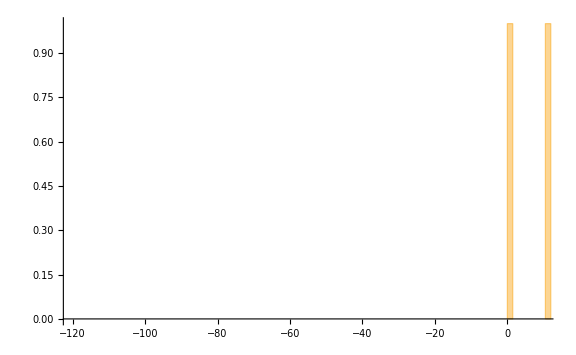

```mathematica
dimD=22;
widths=N[Subdivide[0.01,15,dimD]];
lamd=3;
evlowthreshold=10^-13;

hamm=Table[ham[lamd,widths[[i]],widths[[j]]]/√(norm[widths[[i]],widths[[i]]] norm[widths[[j]],widths[[j]]]),{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]]/√(norm[widths[[i]],widths[[i]]] norm[widths[[j]],widths[[j]]]),{i,dimD},{j,dimD}];

esn=Eigensystem[normm];

(* norm eigensystem in descending eigenvalue order *)
{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[normm]],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(* define transformation such that norm matrix in this basis is the unit matrix Subscript[δ, ij] *)
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

evs=Eigenvalues[normm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<evlowthreshold&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<evlowthreshold&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

(* transfrom Norm *)
trahamN=(Transpose[invtrafma].normm).invtrafma;
normm//MatrixForm;
trahamN//MatrixForm;

(* transfrom Hamiltonian *)
traham=(Transpose[invtrafma].hamm).invtrafma;
traham//MatrixForm;

(* compare results in bare and stable basis spaces and ecce that the stable basis is orthogonal and hence
we solve just an ordinary eigenvalue problem *)
evbare=Sort[Eigensystem[{hamm,normm}][[1]],Re[#1]<Re[#2]&][[;;4]]
evstable=Sort[Eigensystem[traham][[1]],#1<#2&][[;;4]]
Histogram[{evstable,evbare},{1.5},ImageSize->Large,PlotRange->{{-120,10},Automatic},AxesLabel->{MaTeX["E [MeV]",Magnification->2],MaTeX["nbr of EV",Magnification->2]}]
```

```mathematica
IsReal=Select[(#∈Reals)&/@Sort[Eigensystem[{hamm,normm}]][[1]],#==False&];

Print["Norm matrix is positive definite?  ",PositiveDefiniteMatrixQ[normm]]
Print["Hamiltonian is hermitian?  ",HermitianMatrixQ[hamm]]

Print["There are complex eigenvalues?  ",IsReal!={}]
```

(282.883 | -279.101 | -88.5655 | -0.175907
-279.101 | 398.933 | 218.688 | -0.0308305
-88.5655 | 218.688 | 242.721 | 0.629447
-0.175907 | -0.0308305 | 0.629447 | -0.132799)

(1. | 8.99893×10^-9 | 2.46058×10^-9 | 3.13439×10^-12
8.99894×10^-9 | 1. | 5.62842×10^-10 | 3.00436×10^-13
2.46058×10^-9 | 5.62842×10^-10 | 1. | 5.05155×10^-13
3.13439×10^-12 | 3.00435×10^-13 | 5.05156×10^-13 | 1.)

Norm matrix is positive definite?  True

Hamiltonian is hermitian?  True

There are complex eigenvalues?  False